```mathematica
f0 = lw+pw (-g+(p0 g)/(4 √(1/r)));
sol = FullSimplify[DSolve[{y'[x]+l+b y[x]==0,y[0]==y0},y,x]];
solcrit = FullSimplify[DSolve[{y'[x]+l==0,y[0]==y0},y,x]];
solgen = FullSimplify[DSolve[{y'[x]+l*SquareWave[x/2]+b y[x]==0,y[0]==y0},y,x]];
solgencrit = FullSimplify[DSolve[{y'[x]+l*SquareWave[x/2]==0,y[0]==y0},y,x]]
solplot = y[x]/.sol/.y0-> 1/.l-> 1;
solcritplot = y[x]/.solcrit/.y0-> 1/.l-> 1;
solgenplot = Simplify[y[x]/.solgen/.y0-> 1/.l-> 1/.b-> -1]
```

{{y→Function[{x},y0+(Piecewise[{{-l x, 0≤Mod[x/2,1]<1/2}, {l x, True}}])]}}

{Piecewise[{{-1, 2 Mod[x/2,1]≥1||Mod[x/2,1]<0}, {1, True}}]}

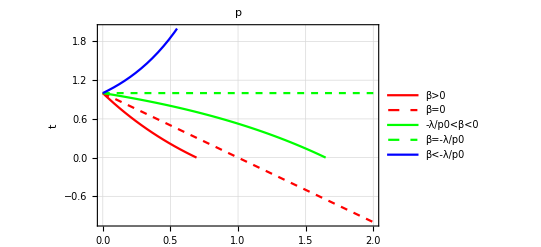

```mathematica
p1 = Plot[solplot/.b-> 1,{x,0,2},PlotRange->{2,0},PlotStyle->Red,PlotLegends-> {"β>0"},Frame->True,GridLines->Automatic];
p2 = Plot[solcritplot,{x,0,2},PlotStyle->{Red,Dashed},PlotLegends-> {"β=0"}];
p3 = Plot[solplot/.b-> -2/3,{x,0,2},PlotRange->{2,0},PlotStyle->Green,PlotLegends-> {"-λ/p0<β<0"}];
p4 = Plot[solplot/.b-> -1,{x,0,2},PlotRange->{2,0},PlotStyle->{Green,Dashed},PlotLegends-> {"β=-λ/p0"}];
p5 = Plot[solplot/.b-> -2,{x,0,2},PlotRange->{2,0},PlotStyle->Blue,PlotLegends-> {"β<-λ/p0"}];
Show[p1,p2,p3,p4,p5,PlotLabel->Style[p,16],AxesLabel->Style[t,16],LabelStyle->Directive[Bold]]
```

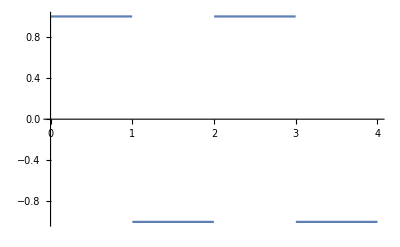

```mathematica
Plot[solgenplot,{x,0,4}]
```

```mathematica
x =1/b(1-Exp[-b*t])
```

(1-ⅇ^(-b t))/b

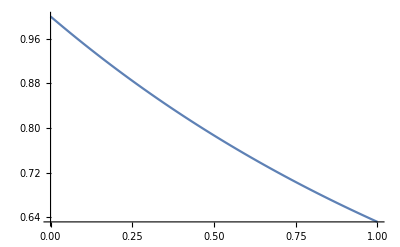

```mathematica
Plot[x/.t-> 1,{b,0,1}]
```

```mathematica
fre = b/2(p+l/(2b))^2+l^2/(2b)
```

l^2/(2 b)+1/2 b (l/(2 b)+p)^2

```mathematica
Simplify[fre]
```

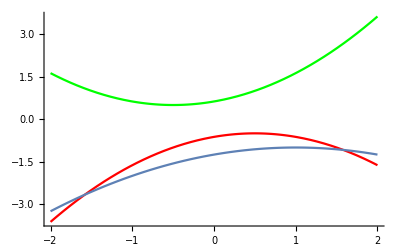

```mathematica
p1 = Plot[l^2/(2 b)+1/2 b (l/(2 b)+p)^2/.l-> 1/.b-> 1,{p,-2,2},PlotRange->All,PlotStyle->Green];
p2 = Plot[l^2/(2 b)+1/2 b (l/(2 b)+p)^2/.l-> 1/.b-> -1,{p,-2,2},PlotStyle-> Red];
p3 = Plot[l^2/(2 b)+1/2 b (l/(2 b)+p)^2/.l-> 1/.b-> -1/2,{p,-2,2}];
Show[p1,p2,p3]
```

```mathematica
solfirst =DSolve[{y'[x]+(b-a) y[x]+a (y[x])^3==0,y[0]== 1},y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y→Function[{x},-(√(a-b) ⅇ^((a-b) (x+Log[1/b]/(2 (a-b)))))/(√(-1+a ⅇ^(2 (a-b) (x+Log[1/b]/(2 (a-b))))))]},{y→Function[{x},(√(a-b) ⅇ^((a-b) (x+Log[1/b]/(2 (a-b)))))/(√(-1+a ⅇ^(2 (a-b) (x+Log[1/b]/(2 (a-b))))))]}}

```mathematica
RootSum[l-a #1+b #1+a #1^3&,Log[-#1+y[x]]/(-a+b+3 a #1^2)&]
```

RootSum[l-a #1+b #1+a #1^3&,Log[-#1+y[x]]/(-a+b+3 a #1^2)&]

```mathematica
yx = y[x]/.solfirst/.a-> a0;
```

```mathematica
Simplify[yx]
```

{-(√(a0-b) ⅇ^((a0-b) (x-C[1])))/(√(-1+a0 ⅇ^(2 (a0-b) (x-C[1])))),(√(a0-b) ⅇ^((a0-b) (x-C[1])))/(√(-1+a0 ⅇ^(2 (a0-b) (x-C[1]))))}

```mathematica
Manipulate[Plot[{-(√(1+b))/(√(-1+(2+b) ⅇ^(2 (1+b) x))),(√(1+b))/(√(-1+(2+b) ⅇ^(2 (1+b) x)))},{x,0,87.32208123916797},PlotRange->Full],{b,-2,2}]
```

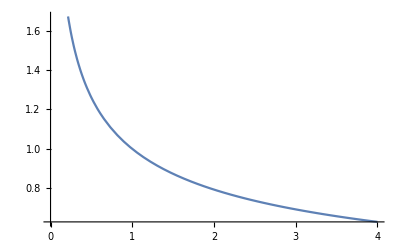

```mathematica
Plot[(1/x)^(1/3),{x,0,4}]
```

```mathematica
GreenFunction[{y'[x]+(b-a) y[x]+a (y[x])^3==0,y[0]== y0,y[100] == 0},y,{x,0,100},y]
```

GreenFunction[{(-a+b) y[x]+a y[x]^3+y'[x]==0,y[0]==y0,y[100]==0},y,{x,0,100},y]

```mathematica
(n-1)/4*Cot[Pi/(n-1)]+(n+1)/4*Cot[Pi/(n+1)]-2*(n)/4*Cot[Pi/(n)]
```

1/4 (-1+n) Cot[π/(-1+n)]-1/2 n Cot[π/n]+1/4 (1+n) Cot[π/(1+n)]

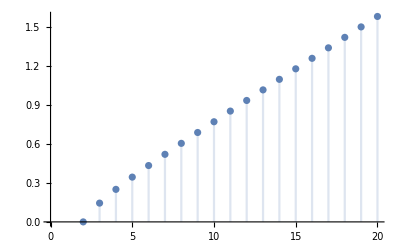

```mathematica
DiscretePlot[1/4  Cot[π/n],{n,2,20}]
```

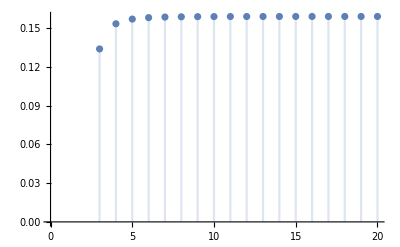

```mathematica
DiscretePlot[-1/2 n Cot[π/n]+1/4 (1+n) Cot[π/(1+n)]+1/4 (n-1) Cot[π/(n-1)],{n,2,20}]
```

```mathematica
phin = -1/2 n Cot[π/n]+1/4 (1+n) Cot[π/(1+n)]+1/4 (n-1) Cot[π/(n-1)];
Simplify[phin]
```

1/4 ((-1+n) Cot[π/(-1+n)]-2 n Cot[π/n]+(1+n) Cot[π/(1+n)])

```mathematica
TrigReduce[1/4 ((-1+n) Cot[π/(-1+n)]-2 n Cot[π/n]+(1+n) Cot[π/(1+n)])]
```

Csc[π/(-1+n)] Csc[π/n] Csc[π/(1+n)] (1/16 Cos[π/(-1+n)-π/n-π/(1+n)]-1/16 ⅈ Sin[π/(-1+n)-π/n-π/(1+n)])+Csc[π/(-1+n)] Csc[π/n] Csc[π/(1+n)] (1/16 Cos[π/(-1+n)-π/n-π/(1+n)]+1/16 ⅈ Sin[π/(-1+n)-π/n-π/(1+n)])+Csc[π/(-1+n)] Csc[π/n] Csc[π/(1+n)] (-1/16 n Cos[π/(-1+n)-π/n-π/(1+n)]-1/16 ⅈ n Sin[π/(-1+n)-π/n-π/(1+n)])+Csc[π/(-1+n)] Csc[π/n] Csc[π/(1+n)] (-1/16 n Cos[π/(-1+n)-π/n-π/(1+n)]+1/16 ⅈ n Sin[π/(-1+n)-π/n-π/(1+n)])+Csc[π/(-1+n)] Csc[π/n] Csc[π/(1+n)] (-1/16 Cos[π/(-1+n)+π/n-π/(1+n)]-1/16 ⅈ Sin[π/(-1+n)+π/n-π/(1+n)])+Csc[π/(-1+n)] Csc[π/n] Csc[π/(1+n)] (-1/16 Cos[π/(-1+n)+π/n-π/(1+n)]+1/16 ⅈ Sin[π/(-1+n)+π/n-π/(1+n)])+Csc[π/(-1+n)] Csc[π/n] Csc[π/(1+n)] (-1/16 n Cos[π/(-1+n)+π/n-π/(1+n)]-1/16 ⅈ n Sin[π/(-1+n)+π/n-π/(1+n)])+Csc[π/(-1+n)] Csc[π/n] Csc[π/(1+n)] (-1/16 n Cos[π/(-1+n)+π/n-π/(1+n)]+1/16 ⅈ n Sin[π/(-1+n)+π/n-π/(1+n)])+Csc[π/(-1+n)] Csc[π/n] Csc[π/(1+n)] (1/8 n Cos[π/(-1+n)-π/n+π/(1+n)]-1/8 ⅈ n Sin[π/(-1+n)-π/n+π/(1+n)])+Csc[π/(-1+n)] Csc[π/n] Csc[π/(1+n)] (1/8 n Cos[π/(-1+n)-π/n+π/(1+n)]+1/8 ⅈ n Sin[π/(-1+n)-π/n+π/(1+n)])

```mathematica
TrigToExp[%51]
```

(ⅈ ⅇ^((ⅈ π)/(-1+n)-(ⅈ π)/n-(ⅈ π)/(1+n)))/(2 (ⅇ^(-(ⅈ π)/(-1+n))-ⅇ^((ⅈ π)/(-1+n))) (ⅇ^(-(ⅈ π)/n)-ⅇ^((ⅈ π)/n)) (ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n))))-(ⅈ ⅇ^((ⅈ π)/(-1+n)+(ⅈ π)/n-(ⅈ π)/(1+n)))/(2 (ⅇ^(-(ⅈ π)/(-1+n))-ⅇ^((ⅈ π)/(-1+n))) (ⅇ^(-(ⅈ π)/n)-ⅇ^((ⅈ π)/n)) (ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n))))-(ⅈ ⅇ^(-(ⅈ π)/(-1+n)-(ⅈ π)/n+(ⅈ π)/(1+n)))/(2 (ⅇ^(-(ⅈ π)/(-1+n))-ⅇ^((ⅈ π)/(-1+n))) (ⅇ^(-(ⅈ π)/n)-ⅇ^((ⅈ π)/n)) (ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n))))+(ⅈ ⅇ^(-(ⅈ π)/(-1+n)+(ⅈ π)/n+(ⅈ π)/(1+n)))/(2 (ⅇ^(-(ⅈ π)/(-1+n))-ⅇ^((ⅈ π)/(-1+n))) (ⅇ^(-(ⅈ π)/n)-ⅇ^((ⅈ π)/n)) (ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n))))-(ⅈ ⅇ^((ⅈ π)/(-1+n)-(ⅈ π)/n-(ⅈ π)/(1+n)) n)/(2 (ⅇ^(-(ⅈ π)/(-1+n))-ⅇ^((ⅈ π)/(-1+n))) (ⅇ^(-(ⅈ π)/n)-ⅇ^((ⅈ π)/n)) (ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n))))+(ⅈ ⅇ^(-(ⅈ π)/(-1+n)+(ⅈ π)/n-(ⅈ π)/(1+n)) n)/((ⅇ^(-(ⅈ π)/(-1+n))-ⅇ^((ⅈ π)/(-1+n))) (ⅇ^(-(ⅈ π)/n)-ⅇ^((ⅈ π)/n)) (ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n))))-(ⅈ ⅇ^((ⅈ π)/(-1+n)+(ⅈ π)/n-(ⅈ π)/(1+n)) n)/(2 (ⅇ^(-(ⅈ π)/(-1+n))-ⅇ^((ⅈ π)/(-1+n))) (ⅇ^(-(ⅈ π)/n)-ⅇ^((ⅈ π)/n)) (ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n))))-(ⅈ ⅇ^(-(ⅈ π)/(-1+n)-(ⅈ π)/n+(ⅈ π)/(1+n)) n)/(2 (ⅇ^(-(ⅈ π)/(-1+n))-ⅇ^((ⅈ π)/(-1+n))) (ⅇ^(-(ⅈ π)/n)-ⅇ^((ⅈ π)/n)) (ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n))))+(ⅈ ⅇ^((ⅈ π)/(-1+n)-(ⅈ π)/n+(ⅈ π)/(1+n)) n)/((ⅇ^(-(ⅈ π)/(-1+n))-ⅇ^((ⅈ π)/(-1+n))) (ⅇ^(-(ⅈ π)/n)-ⅇ^((ⅈ π)/n)) (ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n))))-(ⅈ ⅇ^(-(ⅈ π)/(-1+n)+(ⅈ π)/n+(ⅈ π)/(1+n)) n)/(2 (ⅇ^(-(ⅈ π)/(-1+n))-ⅇ^((ⅈ π)/(-1+n))) (ⅇ^(-(ⅈ π)/n)-ⅇ^((ⅈ π)/n)) (ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n))))

```mathematica
Simplify[%52]
```

(ⅈ (ⅇ^((2 ⅈ π)/(-1+n)) (-1+n)+ⅇ^((2 ⅈ (1+2 n) π)/(n (1+n))) (-1+n)-2 ⅇ^((2 ⅈ π)/n) n-2 ⅇ^((4 ⅈ n π)/(-1+n^2)) n+ⅇ^(2 ⅈ (1/(-1+n)+1/n) π) (1+n)+ⅇ^((2 ⅈ π)/(1+n)) (1+n)))/(2 (-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n))))

```mathematica
ExpToTrig[%53]
```

(ⅈ (-2 n Cos[(2 π)/n]-2 n Cos[(4 n π)/(-1+n^2)]+(-1+n) (Cos[(2 π)/(-1+n)]+ⅈ Sin[(2 π)/(-1+n)])-2 ⅈ n Sin[(2 π)/n]+(1+n) (Cos[(2 π)/(1+n)]+ⅈ Sin[(2 π)/(1+n)])-2 ⅈ n Sin[(4 n π)/(-1+n^2)]+(1+n) (Cos[(2 π)/(-1+n)+(2 π)/n]+ⅈ Sin[(2 π)/(-1+n)+(2 π)/n])+(-1+n) (Cos[(4 π)/(1+n)+(2 π)/(n (1+n))]+ⅈ Sin[(4 π)/(1+n)+(2 π)/(n (1+n))])))/(2 (-1+Cos[(2 π)/(-1+n)]+ⅈ Sin[(2 π)/(-1+n)]) (-1+Cos[(2 π)/n]+ⅈ Sin[(2 π)/n]) (-1+Cos[(2 π)/(1+n)]+ⅈ Sin[(2 π)/(1+n)]))

```mathematica
Simplify[%54]
```

1/16 (-ⅈ+Cot[π/(-1+n)]) (-1-ⅈ Cot[π/n]) (-1-ⅈ Cot[π/(1+n)]) (-2 n Cos[(2 π)/n]-2 n Cos[(4 n π)/(-1+n^2)]+(1+n) (Cos[2 (1/(-1+n)+1/n) π]+ⅈ Sin[2 (1/(-1+n)+1/n) π])+(-1+n) (Cos[(2 π)/(-1+n)]+ⅈ Sin[(2 π)/(-1+n)])-2 ⅈ n Sin[(2 π)/n]+(1+n) (Cos[(2 π)/(1+n)]+ⅈ Sin[(2 π)/(1+n)])-2 ⅈ n Sin[(4 n π)/(-1+n^2)]+(-1+n) (Cos[(2 π+4 n π)/(n+n^2)]+ⅈ Sin[(2 π+4 n π)/(n+n^2)]))

```mathematica
TrigToExp[%55]
```

1/16 (-ⅈ-(ⅈ (ⅇ^(-(ⅈ π)/(-1+n))+ⅇ^((ⅈ π)/(-1+n))))/(ⅇ^(-(ⅈ π)/(-1+n))-ⅇ^((ⅈ π)/(-1+n)))) (-1-(ⅇ^(-(ⅈ π)/n)+ⅇ^((ⅈ π)/n))/(ⅇ^(-(ⅈ π)/n)-ⅇ^((ⅈ π)/n))) (-1-(ⅇ^(-(ⅈ π)/(1+n))+ⅇ^((ⅈ π)/(1+n)))/(ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n)))) ((1/2 (-ⅇ^(-(2 ⅈ π)/(-1+n))+ⅇ^((2 ⅈ π)/(-1+n)))+1/2 (ⅇ^(-(2 ⅈ π)/(-1+n))+ⅇ^((2 ⅈ π)/(-1+n)))) (-1+n)+(1/2 (-ⅇ^(-(ⅈ (2 π+4 n π))/(n+n^2))+ⅇ^((ⅈ (2 π+4 n π))/(n+n^2)))+1/2 (ⅇ^(-(ⅈ (2 π+4 n π))/(n+n^2))+ⅇ^((ⅈ (2 π+4 n π))/(n+n^2)))) (-1+n)+(ⅇ^(-(2 ⅈ π)/n)-ⅇ^((2 ⅈ π)/n)) n-(ⅇ^(-(2 ⅈ π)/n)+ⅇ^((2 ⅈ π)/n)) n+(ⅇ^(-(4 ⅈ n π)/(-1+n^2))-ⅇ^((4 ⅈ n π)/(-1+n^2))) n-(ⅇ^(-(4 ⅈ n π)/(-1+n^2))+ⅇ^((4 ⅈ n π)/(-1+n^2))) n+(1/2 (-ⅇ^(-2 ⅈ (1/(-1+n)+1/n) π)+ⅇ^(2 ⅈ (1/(-1+n)+1/n) π))+1/2 (ⅇ^(-2 ⅈ (1/(-1+n)+1/n) π)+ⅇ^(2 ⅈ (1/(-1+n)+1/n) π))) (1+n)+(1/2 (-ⅇ^(-(2 ⅈ π)/(1+n))+ⅇ^((2 ⅈ π)/(1+n)))+1/2 (ⅇ^(-(2 ⅈ π)/(1+n))+ⅇ^((2 ⅈ π)/(1+n)))) (1+n))

```mathematica
Simplify[%56]
```

(ⅈ (ⅇ^((2 ⅈ π)/(-1+n)) (-1+n)+ⅇ^((2 ⅈ (1+2 n) π)/(n (1+n))) (-1+n)-2 ⅇ^((2 ⅈ π)/n) n-2 ⅇ^((4 ⅈ n π)/(-1+n^2)) n+ⅇ^(2 ⅈ (1/(-1+n)+1/n) π) (1+n)+ⅇ^((2 ⅈ π)/(1+n)) (1+n)))/(2 (-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n))))

```mathematica
GeneratingFunction[%57,n,x]
```

1/2 ⅈ (GeneratingFunction[ⅇ^(2 ⅈ (1/(-1+n)+1/n) π)/((-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n)))),n,x]-GeneratingFunction[ⅇ^((2 ⅈ π)/(-1+n))/((-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n)))),n,x]+GeneratingFunction[ⅇ^((2 ⅈ π)/(1+n))/((-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n)))),n,x]-GeneratingFunction[ⅇ^((2 ⅈ (1+2 n) π)/(n (1+n)))/((-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n)))),n,x]+x GeneratingFunction[(ⅇ^(2 ⅈ (1/(-1+n)+1/n) π) (1+n))/((-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n)))),n,x]+x GeneratingFunction[(ⅇ^((2 ⅈ π)/(-1+n)) (1+n))/((-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n)))),n,x]-2 x GeneratingFunction[(ⅇ^((2 ⅈ π)/n) (1+n))/((-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n)))),n,x]+x GeneratingFunction[(ⅇ^((2 ⅈ π)/(1+n)) (1+n))/((-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n)))),n,x]+x GeneratingFunction[(ⅇ^((2 ⅈ (1+2 n) π)/(n (1+n))) (1+n))/((-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n)))),n,x]-2 x GeneratingFunction[(ⅇ^((4 ⅈ n π)/(-1+n^2)) (1+n))/((-1+ⅇ^((2 ⅈ π)/(-1+n))) (-1+ⅇ^((2 ⅈ π)/n)) (-1+ⅇ^((2 ⅈ π)/(1+n)))),n,x])

```mathematica
N[-3 √3+5/4 √(1+2/(√5))+7/4 Cot[π/7]]-N[1/(2 Pi)]
```

-0.000917521

```mathematica
Expand[Cot[π/(1+n)]]
```

Cot[π/(1+n)]

-(ⅈ (ⅇ^(-(ⅈ π)/(1+n))+ⅇ^((ⅈ π)/(1+n))))/(ⅇ^(-(ⅈ π)/(1+n))-ⅇ^((ⅈ π)/(1+n)))

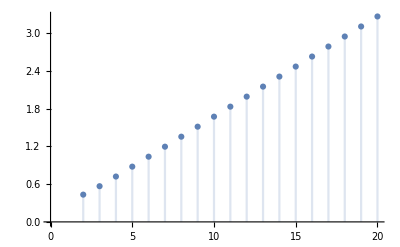

```mathematica
TrigToExp[Cot[π/(1+n)]]
```

```mathematica
z/4  Cot[π/z]
```

1/4 z Cot[π/z]

```mathematica
D[(1/4 z Cot[π/z]), z]
```

1/4 Cot[π/z]+(π Csc[π/z]^2)/(4 z)

```mathematica
D[(1/4 Cot[π/z]+(π Csc[π/z]^2)/(4 z)), z]
```

```mathematica
Limit[(π^2 Cot[π/z] Csc[π/z]^2)/(2 z^3),z-> Infinity]
```

1/(2 π)

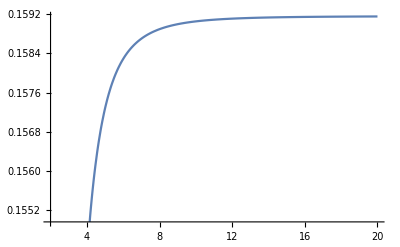

```mathematica
Plot[(π^2 Cot[π/z] Csc[π/z]^2)/(2 z^3),{z,2,20}]
```